| Wert | Fehler
Steigung b | 1.61221 | 0.0188346
Achsenabschnitt a | 0 | 0
Anzahl der Messwerte | 9 | 
Bestimmtheitsmaß R^2 | 0.998581 | 
Die Größe Χ^2/(n - 2) | 1.29496 |

{b→1.61221,Δb→0.0188346,a→0,Δa→0}

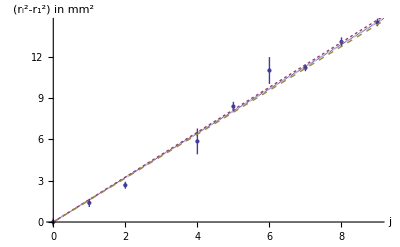

```mathematica
Needs["ErrorBarPlots`"]
data=ReadList["~/gp2/fap/graphen/gruen.tsv",{Real, Real, Real}];

LinReg[data_]:=Module[{x,y,Δy,s,a0,b0,Δa0,Δb0,n,ybar, Nom, DeNom, R,Χ},
n=Length[data];
x=data[[All, 1]];
y=data[[All, 2]];
Δy=data[[All, 3]];

Δa0=0;
a0=0;

b0=(∑_(i=1)^n ((x⟦i⟧*y⟦i⟧)/Δy⟦i⟧^2))/(∑_(i=1)^n (x⟦i⟧^2/Δy⟦i⟧^2));
Χ=√(∑_(i=1)^n ((y[[i]]-b0*x[[i]])/Δy[[i]])^2);
s=√(Χ^2/(n-2));

Δb0=√(1/(∑_(j=1)^n x⟦j⟧^2/Δy⟦j⟧^2));
ybar=1/n*(∑_(i=1)^n y[[i]]/Δy[[i]]^2)/(∑_(i=1)^n 1/Δy[[i]]^2);
Nom =∑_(i=1)^n (y[[i]]-(a0+b0*x[[i]]))^2/Δy[[i]]^2;
DeNom=∑_(i=1)^n (y[[i]]-ybar)^2/Δy[[i]]^2;
R= √(1- Nom/DeNom);

Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0},{"Anzahl der Messwerte", n,""}, {"Bestimmtheitsmaß R^2", R^2, ""}, {"Die Größe Χ^2/(n - 2)",Χ^2/(n-2),""}}]];
{b-> b0,Δb->Δb0, a->a0,Δa->Δa0}

]

regerg=LinReg[data]
Show[ErrorListPlot[data, AxesLabel->{"j", "(r_i^2-r_1^2) in mm^2"}],
Plot[Evaluate[
{b*t+a,(b+Δb)*t+a+Δa,(b-Δb)*t+a-Δa}/.regerg],{t,0,20},
PlotStyle->{Dashing[{0}],Dashing[{0.005}], Dashing[{.01}]}]]
```